# 1. DN - Računalniška orodja v matematiki

#### 1. Analiza z mathematico

Točke od a do j rešite točno in tudi numerično.

a. Definirajte funkcijo .

b. Izračunajte definicijsko območje funkcije .

c. Izračunajte limite funkcije  na robovih definicijskega območja.

d. Izračunajte odvod funkcije .

e. Izračunajte lokalne ekstreme funkcije .

f. Izračunajte intervale naraščanja in padanja funkcije .

g. Narišite graf funkcije  na intervalu [-5, 5].

h. Določite zalogo vrednosti funkcije .

i. Izračunajte nedoločeni integral funkcije .

j. Na 3 decimalke natančno izračunajte volumen vrtenine , ki jo dobimo, če graf funkcije  zavrtimo okoli  osi na intervalu [0.5, 2]. Vrtenino tudi narišite.

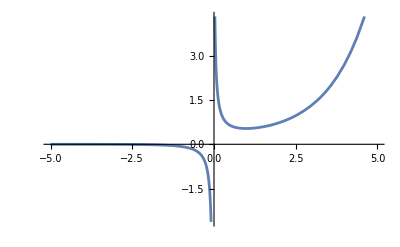

```mathematica
f[x_]:=(E^(x+3))/(100 x+2)
Plot[f[x],{x,-5,5},Exclusions->(-2/100)]
```

```mathematica
domain=Solve[100 x+2!=0,x,Reals]
```

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

{{}}

```mathematica
limLeft=Limit[f[x],x->-2/100,Direction->1]
limRight=Limit[f[x],x->-2/100,Direction->-1]
```

-∞

∞

```mathematica
fDeriv[x_]=D[f[x],x]
```

-(100 ⅇ^(3+x))/(2+100 x)^2+ⅇ^(3+x)/(2+100 x)

```mathematica
criticalPoints=Solve[fDeriv[x]==0,x,Reals]
extrema=Table[{x,f[x]}/. criticalPoints[[i]],{i,Length[criticalPoints]}]
```

{{x→49/50}}

{{49/50,ⅇ^(199/50)/100}}

```mathematica
increasingDecreasing=Reduce[fDeriv[x]>0,x,Reals]
```

x>49/50

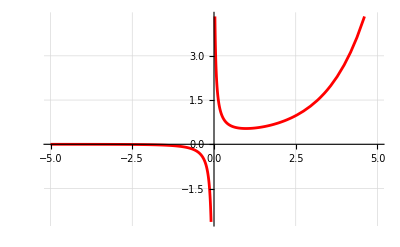

```mathematica
Plot[f[x],{x,-5,5},PlotStyle->Red,GridLines->Automatic]
```

```mathematica
range={MinValue[f[x],x],MaxValue[f[x],x]}
```

{-∞,∞}

```mathematica
indefIntegral=Integrate[f[x],x]
```

1/100 ⅇ^(149/50) ExpIntegralEi[1/50+x]

```mathematica
volume=Pi Integrate[f[x]^2,{x,0.5,2}]
```

1.66479

```mathematica
RevolutionPlot3D[f[x],{x,0.5,2}]
```

-Graphics3D-

#### 2. Splošno o mathematici

a. Pobrišite vrednost vseh spremenljivk, ki ste jih uporabili v prejšnji nalogi.

b. Definirajte funkcijo  in izračunajte njeno vrednost v vseh celih številih med 1 in 100.

c.  Iz seznama dobljenega v nalogi b. izberite zgolj tiste vrednosti, ki imajo na mestu enic praštevilo. Pomagajte si s _?PrimeQ in MemberQ.

d. Definirajte anonimno funkcijo, ki kvadrira število in mu prišteje 1 in jo uporabite na zgoraj dobljenem seznamu.

e. Seznam iz prejšnje naloge zaokrožite navzdol in seštejte vsa tista števila, ki so deliva s 3.

```mathematica
ClearAll[x,y,izraz,g,seznam,f,pravilo]
```

```mathematica
g[x_]:=(1+x^2.1)/(3+x)
```

```mathematica
Function[x,(1+x^2.1)/(3+x)]
```

Function[x,(1+x^2.1)/(3+x)]

```mathematica
vrednosti=Table[g[x],{x,1,100}]
```

{0.5,1.05742,1.84085,2.76845,3.79568,4.89604,6.05259,7.25393,8.49202,9.76096,11.0563,12.3747,13.7134,15.0702,16.4433,17.8313,19.2328,20.6469,22.0727,23.5093,24.956,26.4123,27.8776,29.3514,30.8333,32.3228,33.8198,35.3238,36.8345,38.3516,39.875,41.4044,42.9396,44.4803,46.0265,47.5778,49.1343,50.6956,52.2618,53.8326,55.4079,56.9876,58.5716,60.1598,61.7521,63.3483,64.9485,66.5525,68.1602,69.7716,71.3865,73.005,74.6269,76.2521,77.8807,79.5125,81.1475,82.7856,84.4268,86.0711,87.7183,89.3684,91.0214,92.6772,94.3359,95.9972,97.6613,99.3281,100.997,102.669,104.344,106.021,107.7,109.382,111.067,112.754,114.443,116.134,117.828,119.524,121.222,122.923,124.625,126.33,128.037,129.746,131.457,133.171,134.886,136.603,138.322,140.044,141.767,143.492,145.219,146.948,148.679,150.412,152.146,153.883}

```mathematica
seznam=Select[vrednosti,PrimeQ[Mod[Round[#],10]]&]
```

{1.84085,2.76845,4.89604,7.25393,12.3747,15.0702,22.0727,24.956,32.3228,35.3238,36.8345,42.9396,52.2618,55.4079,56.9876,61.7521,63.3483,64.9485,66.5525,73.005,74.6269,82.7856,92.6772,102.669,112.754,122.923,124.625,133.171,134.886,136.603,141.767,143.492,145.219,146.948,152.146}

```mathematica
kvadratPlus1=#^2+1&;
```

```mathematica
#1^2+1&
```

#1^2+1&

```mathematica
novSeznam=kvadratPlus1/@seznam
```

{4.38873,8.66433,24.9712,53.6195,154.134,228.11,488.203,623.802,1045.77,1248.77,1357.78,1844.81,2732.29,3071.03,3248.59,3814.32,4014.01,4219.31,4430.24,5330.73,5570.17,6854.46,8590.07,10542.,12714.4,15111.,15532.5,17735.4,18195.2,18661.4,20098.9,20591.,21089.6,21594.8,23149.5}

```mathematica
zaokrozenSeznam=Floor/@novSeznam
vsota=Total[Select[zaokrozenSeznam,Mod[#,3]==0&]]
```

{4,8,24,53,154,228,488,623,1045,1248,1357,1844,2732,3071,3248,3814,4014,4219,4430,5330,5570,6854,8590,10542,12714,15110,15532,17735,18195,18661,20098,20590,21089,21594,23149}

68559

#### 3. Prepisovalna pravila

```mathematica
Clear[x, y, izraz]
izraz = x^2 + 2x + 1
```

a. Definirajte prepisovalno pravilo, ki  v izrazu vse pojavitve x zamenja z y + 1.

b. Z uporabo prepisovalnih pravil izračunajte vrednost izraza za  x = 2

c. Definirajte funkcija  in s pomočjo prepisovalnih pravil zamenjajte vse pojavitve  v

d. Prepisovalno pravilo iz naloge c uporabite na funkciji ,  kolikokrat gre.

e. Definiraj prepisovalna pravila, s pomočjo katerih lahko izračunate poljuben člen fibonaccijevega zaporedja, z začetkom `Fib[10]`

```mathematica
pravilo=x->y+1
```

x→1+y

```mathematica
izraz=x^2+2 x+1
vrednostIzraza=izraz/. x->2
```

1+2 x+x^2

9

```mathematica
f[x_]:=x^5-4 x^3+x^2+3 x-2
novoPravilo=x^n_->2 n x^(n-1)
novaFunkcija=f[x]/. novoPravilo
```

x^n_→2 n x^(-1+n)

-2+7 x-24 x^2+10 x^4

```mathematica
gPravilo=x^n_->2 n x^(n-1)
novaG=x^2025/. gPravilo
```

x^n_→2 n x^(-1+n)

4050 x^2024

```mathematica
FibRule={Fib[0]->0,Fib[1]->1,Fib[n_]:>Fib[n-1]+Fib[n-2]}
Fib[10]/. FibRule//FullSimplify
```

{Fib[0]→0,Fib[1]→1,Fib[n_]:>Fib[n-1]+Fib[n-2]}

Fib[8]+Fib[9]